```mathematica
LifeGame[n_Integer?Positive, steps_]:=
Module[{gameboard, liveNeighbors, update},
gameboard=Table[Random[Integer], {n}, {n}];
liveNeighbors[mat_]:=
Apply[Plus, Map[RotateRight[mat, #] &,
{{-1,-1}, {-1,0}, {-1,1}, {0,-1},
{0,1}, {1,-1}, {1,0}, {1,1}}]];
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update, Listable];
FixedPointList[
update[#, liveNeighbors[#]]&, gameboard, steps]
]
```

```mathematica
g=LifeGame[100,150];
```

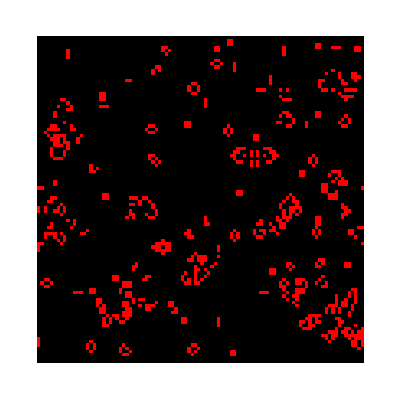

```mathematica
ArrayPlot[Last[g],ColorRules->{0->Black,1->Red}]
```